```mathematica
G := SetPrecision[6.674*10^(-8), 80] (*en cgs*)
c := SetPrecision[2.998*10^(10), 80](*en cgs*)
ti :=SetPrecision[ 1.48*10^(12), 80](*s*)
ρt :=SetPrecisiregula_falsion[ 100, 80] (*cgs *)
hbar :=SetPrecision[ 1.05*10^(-27), 80] (*cgs*)
```

```mathematica
ρcrit1[x_] := ((ρt +√(ρt^2 -4*(x^2*ρt)/((1+x^2)^3)))(1+x^2)^3)/(2*x^2)
```

```mathematica
ρcrit2[x_] := ((ρt -√(ρt^2 -4*(x^2*ρt)/((1+x^2)^3)))(1+x^2)^3)/(2*x^2)
```

```mathematica
func[x_] := SetPrecision[1/2 √((3 c^2)/(8π G ρcrit1[x]))(ArcSinh[x]+x √(1+x^2))-ti, 80]
```

```mathematica
FindRoot[func[x],{x,10^10`80},WorkingPrecision->80]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 80. digits of working precision to meet these tolerances.

{x→1.0000000000000000000000000000000000000018367099233434952235171332625298739555328×10^10}

```mathematica
NSolve[func[x]==0, x]
```

$Aborted

```mathematica
γ := 0.2375
ρcrit = (√3 c^7)/(16*π^2*γ^3*G^2*hbar)
```

3.81074×10^114

```mathematica
fun[x_]:= 1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1))-ti
```

```mathematica
NSolve[fun[x]==0, x]
```

$Aborted

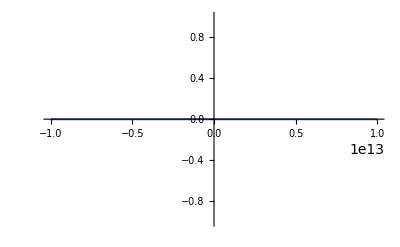

```mathematica
Plot[fun[x]+ti, {x, -10^13, 10^13}]
```

```mathematica
FindRoot[1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1)), {x, 0}]
```

{x→0.}

```mathematica
Limit[1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1)) -> ∞]
```

Limit::argtu: Limit called with 1 argument; 2 or 3 arguments are expected.

```mathematica
Limit[1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1)) ,x->∞]
```

∞

```mathematica
Limit[1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1)) ,x->-∞]
```

-∞

```mathematica
ver[x_]:=1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1))-ti 
ver[10^30]
```

1.02679×10^16

```mathematica
FindRoot[1/2 √((3*c^2)/(8*π*G*ρcrit))(ArcSinh[x]+x*√(x^2+1))-ti, {x, 10^30}, WorkingPrecision->50,AccuracyGoal->20,PrecisionGoal->20]
```

FindRoot::precw: The precision of the argument function (-1.48×10^12+1.02694×10^-44 (x √(1+x^2)+ArcSinh[x])) is less than WorkingPrecision (50.).

{x→1.2004903722253255843948491234674162692898767405791×10^28}

```mathematica
ver[1.200490372225325584394849123467416269289876740579126858498872439321`50.*^28]
```

0.

```mathematica
xi:=1.200490372225325584394849123467416269289876740579126858498872439321`50.*^28
```

```mathematica
ab :=( 2.9*10^(-4))/(1+xi^2)^(1/2)
ab
```

2.41568×10^-32

```mathematica
ηb := √((8π G ab^2 ρcrit)/(3c^2))
ηb
```

1.17616×10^12